## Notebook for Homework 1

#### Get the Data

This is the location of the data on an Excel file:

```mathematica
originalFile="/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/Boston2017Hourly.xlsx";
```

```mathematica
(*originalFile2 = "/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/EnergyJuneMA.xlsx"*)
```

We need to import the data into a variable and then cleanup

```mathematica
sheet=First@Import[originalFile];
```

```mathematica
headers=First@sheet
```

{DateHour,Actual}

```mathematica
data=Map[AssociationThread[headers->#]&,Rest@sheet]
```

{<|DateHour→Sun 1 Jan 2017 00:00:00GMT-4.,Actual→1542.56|>,<|DateHour→Sun 1 Jan 2017 01:00:00GMT-4.,Actual→1436.88|>,<|DateHour→Sun 1 Jan 2017 01:59:59GMT-4.,Actual→1401.3|>,<|DateHour→Sun 1 Jan 2017 02:59:59GMT-4.,Actual→1433.75|>,8751,<|DateHour→Sun 31 Dec 2017 18:59:16GMT-4.,Actual→2404.78|>,<|DateHour→Sun 31 Dec 2017 19:59:16GMT-4.,Actual→2293.56|>,<|DateHour→Sun 31 Dec 2017 20:59:16GMT-4.,Actual→2178.72|>,<|DateHour→Sun 31 Dec 2017 21:59:16GMT-4.,Actual→1769.91|>}
 |  |  |  |

```mathematica
data1=Rule@@@data[[All,{"DateHour","Actual"}]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 01:59:59GMT-4.→1401.3,Sun 1 Jan 2017 02:59:59GMT-4.→1433.75,Sun 1 Jan 2017 03:59:59GMT-4.→1384.62,Sun 1 Jan 2017 04:59:59GMT-4.→1458.61,8747,Sun 31 Dec 2017 16:59:16GMT-4.→2588.58,Sun 31 Dec 2017 17:59:16GMT-4.→2490.11,Sun 31 Dec 2017 18:59:16GMT-4.→2404.78,Sun 31 Dec 2017 19:59:16GMT-4.→2293.56,Sun 31 Dec 2017 20:59:16GMT-4.→2178.72,Sun 31 Dec 2017 21:59:16GMT-4.→1769.91}
 |  |  |  |

I want to use the first 14 days of the month for training, therefore I have to cut the dataset to only the first 9 months = 6554 hours

```mathematica
trainingset=data1[[1;;]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 01:59:59GMT-4.→1401.3,Sun 1 Jan 2017 02:59:59GMT-4.→1433.75,Sun 1 Jan 2017 03:59:59GMT-4.→1384.62,Sun 1 Jan 2017 04:59:59GMT-4.→1458.61,8747,Sun 31 Dec 2017 16:59:16GMT-4.→2588.58,Sun 31 Dec 2017 17:59:16GMT-4.→2490.11,Sun 31 Dec 2017 18:59:16GMT-4.→2404.78,Sun 31 Dec 2017 19:59:16GMT-4.→2293.56,Sun 31 Dec 2017 20:59:16GMT-4.→2178.72,Sun 31 Dec 2017 21:59:16GMT-4.→1769.91}
 |  |  |  |

```mathematica
validationset = data1[[-24*31;; ]]
```

{Thu 30 Nov 2017 22:59:19GMT-4.→1555.37,Thu 30 Nov 2017 23:59:19GMT-4.→1451.37,Fri 1 Dec 2017 00:59:19GMT-4.→1395.16,Fri 1 Dec 2017 01:59:19GMT-4.→1387.24,Fri 1 Dec 2017 02:59:19GMT-4.→1446.83,Fri 1 Dec 2017 03:59:19GMT-4.→1702.98,732,Sun 31 Dec 2017 16:59:16GMT-4.→2588.58,Sun 31 Dec 2017 17:59:16GMT-4.→2490.11,Sun 31 Dec 2017 18:59:16GMT-4.→2404.78,Sun 31 Dec 2017 19:59:16GMT-4.→2293.56,Sun 31 Dec 2017 20:59:16GMT-4.→2178.72,Sun 31 Dec 2017 21:59:16GMT-4.→1769.91}
 |  |  |  |

#### Train a Neural Network

```mathematica
p = Predict[trainingset,Method->"NeuralNetwork"]
```

PredictorFunction[…]

We test the network and see how it predicts for the next 24 hours

```mathematica
test = Table[DateObject[{2017, 12, 1, i, 0, 0.}], {i, 0, 24*31}];
```

```mathematica
forecast = p[test];
```

```mathematica
actual = validationset[[All, 2]];
```

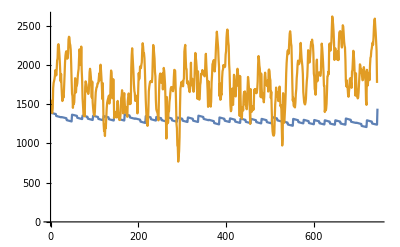

```mathematica
ListLinePlot[{forecast,actual}]
```

```mathematica
dist=p[test,"Distribution"][[1]]
```

NormalDistribution[1387.95,538.509]

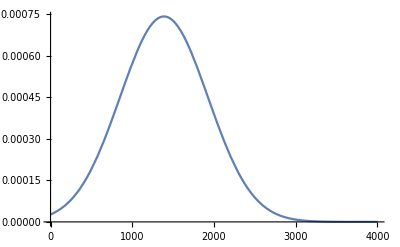

```mathematica
Plot[PDF[dist,x],{x,0,4000},PlotRange->All]
```